(0.1 ⅇ^(100. (-1+x)))/(1-2.2711×10^-14 x)

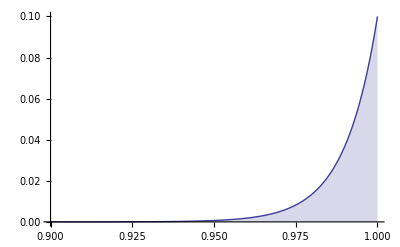

```mathematica
p[x_]:=μ f[x]/(1-k w[x]) (*turelli 1984, 3.2a*)
k=Exp[-μ π Vs/m^2];(*turelli 1984, 3.9*)
fs[s_,so_,λ_,n_]:=2/λ PDF[NoncentralChiSquareDistribution[n,(2so)/λ],2/λ(so-s)]HeavisideTheta[so-s];
f[x_]:=Simplify[fs[s,so,λ,n]/.s->x-mwt/.so->mmax-mwt,{mmax>x,λ>0}]
w[x_]:=x
p[x]/.mmax->1/.mwt->1/.m->λ/.λ->2Es/n/.Ex->0.01/.n->2/.Vs->1/.μ->0.001/.Es->0.01
Plot[%,{x,0.9,1},Filling->0,PlotRange->All]
```

```mathematica
p[w_]:=μ g[w]/(1-k w) (*turelli 1984 3.2a, with trait value x equal to fitness w*)
k=Exp[-μ π Vs/m^2]/.Vs->1/.m->;(*turelli 1984 3.9, with Vs = ω^2+Ve = 1+0 = 1 and m the variance in fitness of new mutants*)

fs[s_,so_,λ_,n_]:=2/λ PDF[NoncentralChiSquareDistribution[n,(2so)/λ],2/λ(so-s)]HeavisideTheta[so-s];
g[w_]:=Simplify[fs[s,so,λ,n]/.s->w-mwt/.so->mmax-mwt,{mmax>w,λ>0}]


p[x]
Plot[%,{x,0.9,1},Filling->0,PlotRange->All]
```

```mathematica
Clear[w]
```

```mathematica
fs[s_,so_,λ_,n_]:=2/λ PDF[NoncentralChiSquareDistribution[n,(2so)/λ],2/λ(so-s)]HeavisideTheta[so-s];
g[w_]:=Simplify[fs[s,so,λ,n]/.s->w-1/.so->0,{w<1,λ>0}]
```

```mathematica
g[w]
```

(ⅇ^((-1+w)/λ) ((1-w)/λ)^(1/2 (-2+n)))/(λ Gamma[n/2])

-(ⅇ^((-1+w)/λ) ((1-w)/λ)^(1/2 (-2+n)) μ)/((-1+w) λ Gamma[n/2])

-(0.2 ⅇ^(200. (-1+w)))/(-1+w)

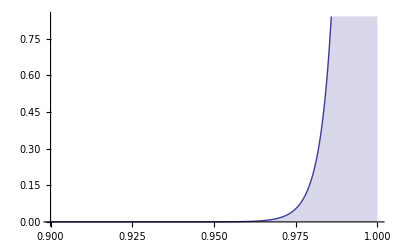

```mathematica
(μ g[w])/-s/.s->w-1
%/.μ->0.001/.λ->0.005/.n->2
Plot[%,{w,0.9,1},Filling->0]
```

```mathematica
Clear[g,w,sol]
```

```mathematica
g[x1_,x2_]:=(ⅇ^(1/2 (-x1^2/λ-x2^2/λ)))/(2 π √(λ^2))
w[x1_,x2_]:=ⅇ^(1/2 (-x1^2-x2^2))
```

```mathematica
sol=Simplify[Solve[{p[x1,x2]==(μ g[x1,x2])/(1-k w[x1,x2])}/.k->(1-μ)/Integrate[p[x1,x2]w[x1,x2],{x1,-∞,∞},{x2,-∞,∞}],p[x1,x2]],λ>0]
```

{{p[x1,x2]→0},{p[x1,x2]→(ⅇ^(-((x1^2+x2^2) (1+λ))/(2 λ)) (-ⅇ^((x1^2+x2^2)/(2 λ)) λ (-1+μ)+ⅇ^(1/2 (x1^2+x2^2)) μ))/(2 π λ)}}

```mathematica
p[x1,x2]/.sol[[2]]/.λ->0.005/.μ->0.0001
Plot3D[%,{x1,-3,3},{x2,-3,3},PlotRange->{0,0.2}]
```

31.831 ⅇ^(-100.5 (x1^2+x2^2)) (0.0001 ⅇ^(1/2 (x1^2+x2^2))+0.0049995 ⅇ^(100. (x1^2+x2^2)))

-Graphics3D-

```mathematica
Integrate[p[x1,x2]/.sol,{x1,-∞,∞},{x2,-∞,∞},Assumptions->λ>0]
```

{0,1}

```mathematica
Simplify[Integrate[p[x1,x2]w[x1,x2],{x1,-∞,∞},{x2,-∞,∞}]/.sol[[2]],λ>0]
%/.λ->0/.μ->0.
```

(1+λ+μ-λ μ)/(2+2 λ)

0.5